```mathematica
1/(4*500000)==0.0000005
```

True

```mathematica
area[μ_,σ_,α_]:=NIntegrate[PDF[SkewNormalDistribution[μ,σ,α],s],{s,0.0000005,10*σ}]
```

```mathematica
μ={-0.0500000000000000,-0.0372751426827093,-0.0277887252403267,-0.0207165739660756,-0.0154442650096474,-0.0115137436372836,-0.0085835287378376,-0.0063990451684807,-0.0047705064337644,-0.0035564261597470,-0.0026513258509018,-0.0019765709878144,-0.0014735393118657,-0.0010985277619675,-0.0008189555813651,-0.0006105337229237,-0.0004551546326917,-0.0003393190775256,-0.0002529633405947,-0.0001885848922832,-0.0001405905753532,-0.0001048106751227,-0.0000781366573974,-0.0000582511010648,-0.0000434263620723,-0.0000323744768487,-0.0000241352648763,-0.0000179929088390,-0.0000134137648850,-0.0000100000000000};
```

```mathematica
σ={0.0000100000000000,0.0000134137648850,0.0000179929088390,0.0000241352648763,0.0000323744768487,0.0000434263620723,0.0000582511010648,0.0000781366573974,0.0001048106751227,0.0001405905753532,0.0001885848922832,0.0002529633405947,0.0003393190775256,0.0004551546326917,0.0006105337229237,0.0008189555813651,0.0010985277619675,0.0014735393118657,0.0019765709878144,0.0026513258509018,0.0035564261597470,0.0047705064337644,0.0063990451684807,0.0085835287378376,0.0115137436372836,0.0154442650096474,0.0207165739660756,0.0277887252403267,0.0372751426827093,0.0500000000000000};
```

```mathematica
area0=Table[{μ[[i]],σ[[j]],0,Chop[area[μ[[i]],σ[[j]],0]]},{i,1,30},{j,1,30}];
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver22/dfe_area_5e-7-inf_alpha=0.csv",area0]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver22/dfe_area_5e-7-inf_alpha=0.csv

```mathematica
area2=Table[{μ[[i]],σ[[j]],-2,Chop[area[μ[[i]],σ[[j]],-2]]},{i,1,30},{j,1,30}];
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver22/dfe_area_5e-7-inf_alpha=-2.csv",area2]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver22/dfe_area_5e-7-inf_alpha=-2.csv

```mathematica
area4=Table[{μ[[i]],σ[[j]],-4,Chop[area[μ[[i]],σ[[j]],-4]]},{i,1,30},{j,1,30}];
Export["/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver22/dfe_area_5e-7-inf_alpha=-4.csv",area4]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

/Users/alyulina/Projects/Kondrashov/Sandpiper/h=sigm/ver22/dfe_area_5e-7-inf_alpha=-4.csv

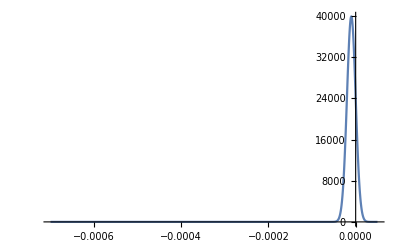

```mathematica
Plot[PDF[SkewNormalDistribution[-0.00001,0.00001,0],s],{s,-0.0007,0.00005},PlotRange->All]
```